# Wilson Graph

## Wilson’s Theorem

```mathematica
circleLayout[n_]:=Table[{Cos[2π/n i],Sin[2π/n i]},{i,n}];
```

```mathematica
Table[Mod[i*j,n],{i,1,n-1},{j,1,n-1}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37 | 39
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36 | 39 | 1 | 4 | 7 | 10 | 13 | 16 | 19 | 22 | 25 | 28 | 31 | 34 | 37 | 40 | 2 | 5 | 8 | 11 | 14 | 17 | 20 | 23 | 26 | 29 | 32 | 35 | 38
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 3 | 7 | 11 | 15 | 19 | 23 | 27 | 31 | 35 | 39 | 2 | 6 | 10 | 14 | 18 | 22 | 26 | 30 | 34 | 38 | 1 | 5 | 9 | 13 | 17 | 21 | 25 | 29 | 33 | 37
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 4 | 9 | 14 | 19 | 24 | 29 | 34 | 39 | 3 | 8 | 13 | 18 | 23 | 28 | 33 | 38 | 2 | 7 | 12 | 17 | 22 | 27 | 32 | 37 | 1 | 6 | 11 | 16 | 21 | 26 | 31 | 36
6 | 12 | 18 | 24 | 30 | 36 | 1 | 7 | 13 | 19 | 25 | 31 | 37 | 2 | 8 | 14 | 20 | 26 | 32 | 38 | 3 | 9 | 15 | 21 | 27 | 33 | 39 | 4 | 10 | 16 | 22 | 28 | 34 | 40 | 5 | 11 | 17 | 23 | 29 | 35
7 | 14 | 21 | 28 | 35 | 1 | 8 | 15 | 22 | 29 | 36 | 2 | 9 | 16 | 23 | 30 | 37 | 3 | 10 | 17 | 24 | 31 | 38 | 4 | 11 | 18 | 25 | 32 | 39 | 5 | 12 | 19 | 26 | 33 | 40 | 6 | 13 | 20 | 27 | 34
8 | 16 | 24 | 32 | 40 | 7 | 15 | 23 | 31 | 39 | 6 | 14 | 22 | 30 | 38 | 5 | 13 | 21 | 29 | 37 | 4 | 12 | 20 | 28 | 36 | 3 | 11 | 19 | 27 | 35 | 2 | 10 | 18 | 26 | 34 | 1 | 9 | 17 | 25 | 33
9 | 18 | 27 | 36 | 4 | 13 | 22 | 31 | 40 | 8 | 17 | 26 | 35 | 3 | 12 | 21 | 30 | 39 | 7 | 16 | 25 | 34 | 2 | 11 | 20 | 29 | 38 | 6 | 15 | 24 | 33 | 1 | 10 | 19 | 28 | 37 | 5 | 14 | 23 | 32
10 | 20 | 30 | 40 | 9 | 19 | 29 | 39 | 8 | 18 | 28 | 38 | 7 | 17 | 27 | 37 | 6 | 16 | 26 | 36 | 5 | 15 | 25 | 35 | 4 | 14 | 24 | 34 | 3 | 13 | 23 | 33 | 2 | 12 | 22 | 32 | 1 | 11 | 21 | 31
11 | 22 | 33 | 3 | 14 | 25 | 36 | 6 | 17 | 28 | 39 | 9 | 20 | 31 | 1 | 12 | 23 | 34 | 4 | 15 | 26 | 37 | 7 | 18 | 29 | 40 | 10 | 21 | 32 | 2 | 13 | 24 | 35 | 5 | 16 | 27 | 38 | 8 | 19 | 30
12 | 24 | 36 | 7 | 19 | 31 | 2 | 14 | 26 | 38 | 9 | 21 | 33 | 4 | 16 | 28 | 40 | 11 | 23 | 35 | 6 | 18 | 30 | 1 | 13 | 25 | 37 | 8 | 20 | 32 | 3 | 15 | 27 | 39 | 10 | 22 | 34 | 5 | 17 | 29
13 | 26 | 39 | 11 | 24 | 37 | 9 | 22 | 35 | 7 | 20 | 33 | 5 | 18 | 31 | 3 | 16 | 29 | 1 | 14 | 27 | 40 | 12 | 25 | 38 | 10 | 23 | 36 | 8 | 21 | 34 | 6 | 19 | 32 | 4 | 17 | 30 | 2 | 15 | 28
14 | 28 | 1 | 15 | 29 | 2 | 16 | 30 | 3 | 17 | 31 | 4 | 18 | 32 | 5 | 19 | 33 | 6 | 20 | 34 | 7 | 21 | 35 | 8 | 22 | 36 | 9 | 23 | 37 | 10 | 24 | 38 | 11 | 25 | 39 | 12 | 26 | 40 | 13 | 27
15 | 30 | 4 | 19 | 34 | 8 | 23 | 38 | 12 | 27 | 1 | 16 | 31 | 5 | 20 | 35 | 9 | 24 | 39 | 13 | 28 | 2 | 17 | 32 | 6 | 21 | 36 | 10 | 25 | 40 | 14 | 29 | 3 | 18 | 33 | 7 | 22 | 37 | 11 | 26
16 | 32 | 7 | 23 | 39 | 14 | 30 | 5 | 21 | 37 | 12 | 28 | 3 | 19 | 35 | 10 | 26 | 1 | 17 | 33 | 8 | 24 | 40 | 15 | 31 | 6 | 22 | 38 | 13 | 29 | 4 | 20 | 36 | 11 | 27 | 2 | 18 | 34 | 9 | 25
17 | 34 | 10 | 27 | 3 | 20 | 37 | 13 | 30 | 6 | 23 | 40 | 16 | 33 | 9 | 26 | 2 | 19 | 36 | 12 | 29 | 5 | 22 | 39 | 15 | 32 | 8 | 25 | 1 | 18 | 35 | 11 | 28 | 4 | 21 | 38 | 14 | 31 | 7 | 24
18 | 36 | 13 | 31 | 8 | 26 | 3 | 21 | 39 | 16 | 34 | 11 | 29 | 6 | 24 | 1 | 19 | 37 | 14 | 32 | 9 | 27 | 4 | 22 | 40 | 17 | 35 | 12 | 30 | 7 | 25 | 2 | 20 | 38 | 15 | 33 | 10 | 28 | 5 | 23
19 | 38 | 16 | 35 | 13 | 32 | 10 | 29 | 7 | 26 | 4 | 23 | 1 | 20 | 39 | 17 | 36 | 14 | 33 | 11 | 30 | 8 | 27 | 5 | 24 | 2 | 21 | 40 | 18 | 37 | 15 | 34 | 12 | 31 | 9 | 28 | 6 | 25 | 3 | 22
20 | 40 | 19 | 39 | 18 | 38 | 17 | 37 | 16 | 36 | 15 | 35 | 14 | 34 | 13 | 33 | 12 | 32 | 11 | 31 | 10 | 30 | 9 | 29 | 8 | 28 | 7 | 27 | 6 | 26 | 5 | 25 | 4 | 24 | 3 | 23 | 2 | 22 | 1 | 21
21 | 1 | 22 | 2 | 23 | 3 | 24 | 4 | 25 | 5 | 26 | 6 | 27 | 7 | 28 | 8 | 29 | 9 | 30 | 10 | 31 | 11 | 32 | 12 | 33 | 13 | 34 | 14 | 35 | 15 | 36 | 16 | 37 | 17 | 38 | 18 | 39 | 19 | 40 | 20
22 | 3 | 25 | 6 | 28 | 9 | 31 | 12 | 34 | 15 | 37 | 18 | 40 | 21 | 2 | 24 | 5 | 27 | 8 | 30 | 11 | 33 | 14 | 36 | 17 | 39 | 20 | 1 | 23 | 4 | 26 | 7 | 29 | 10 | 32 | 13 | 35 | 16 | 38 | 19
23 | 5 | 28 | 10 | 33 | 15 | 38 | 20 | 2 | 25 | 7 | 30 | 12 | 35 | 17 | 40 | 22 | 4 | 27 | 9 | 32 | 14 | 37 | 19 | 1 | 24 | 6 | 29 | 11 | 34 | 16 | 39 | 21 | 3 | 26 | 8 | 31 | 13 | 36 | 18
24 | 7 | 31 | 14 | 38 | 21 | 4 | 28 | 11 | 35 | 18 | 1 | 25 | 8 | 32 | 15 | 39 | 22 | 5 | 29 | 12 | 36 | 19 | 2 | 26 | 9 | 33 | 16 | 40 | 23 | 6 | 30 | 13 | 37 | 20 | 3 | 27 | 10 | 34 | 17
25 | 9 | 34 | 18 | 2 | 27 | 11 | 36 | 20 | 4 | 29 | 13 | 38 | 22 | 6 | 31 | 15 | 40 | 24 | 8 | 33 | 17 | 1 | 26 | 10 | 35 | 19 | 3 | 28 | 12 | 37 | 21 | 5 | 30 | 14 | 39 | 23 | 7 | 32 | 16
26 | 11 | 37 | 22 | 7 | 33 | 18 | 3 | 29 | 14 | 40 | 25 | 10 | 36 | 21 | 6 | 32 | 17 | 2 | 28 | 13 | 39 | 24 | 9 | 35 | 20 | 5 | 31 | 16 | 1 | 27 | 12 | 38 | 23 | 8 | 34 | 19 | 4 | 30 | 15
27 | 13 | 40 | 26 | 12 | 39 | 25 | 11 | 38 | 24 | 10 | 37 | 23 | 9 | 36 | 22 | 8 | 35 | 21 | 7 | 34 | 20 | 6 | 33 | 19 | 5 | 32 | 18 | 4 | 31 | 17 | 3 | 30 | 16 | 2 | 29 | 15 | 1 | 28 | 14
28 | 15 | 2 | 30 | 17 | 4 | 32 | 19 | 6 | 34 | 21 | 8 | 36 | 23 | 10 | 38 | 25 | 12 | 40 | 27 | 14 | 1 | 29 | 16 | 3 | 31 | 18 | 5 | 33 | 20 | 7 | 35 | 22 | 9 | 37 | 24 | 11 | 39 | 26 | 13
29 | 17 | 5 | 34 | 22 | 10 | 39 | 27 | 15 | 3 | 32 | 20 | 8 | 37 | 25 | 13 | 1 | 30 | 18 | 6 | 35 | 23 | 11 | 40 | 28 | 16 | 4 | 33 | 21 | 9 | 38 | 26 | 14 | 2 | 31 | 19 | 7 | 36 | 24 | 12
30 | 19 | 8 | 38 | 27 | 16 | 5 | 35 | 24 | 13 | 2 | 32 | 21 | 10 | 40 | 29 | 18 | 7 | 37 | 26 | 15 | 4 | 34 | 23 | 12 | 1 | 31 | 20 | 9 | 39 | 28 | 17 | 6 | 36 | 25 | 14 | 3 | 33 | 22 | 11
31 | 21 | 11 | 1 | 32 | 22 | 12 | 2 | 33 | 23 | 13 | 3 | 34 | 24 | 14 | 4 | 35 | 25 | 15 | 5 | 36 | 26 | 16 | 6 | 37 | 27 | 17 | 7 | 38 | 28 | 18 | 8 | 39 | 29 | 19 | 9 | 40 | 30 | 20 | 10
32 | 23 | 14 | 5 | 37 | 28 | 19 | 10 | 1 | 33 | 24 | 15 | 6 | 38 | 29 | 20 | 11 | 2 | 34 | 25 | 16 | 7 | 39 | 30 | 21 | 12 | 3 | 35 | 26 | 17 | 8 | 40 | 31 | 22 | 13 | 4 | 36 | 27 | 18 | 9
33 | 25 | 17 | 9 | 1 | 34 | 26 | 18 | 10 | 2 | 35 | 27 | 19 | 11 | 3 | 36 | 28 | 20 | 12 | 4 | 37 | 29 | 21 | 13 | 5 | 38 | 30 | 22 | 14 | 6 | 39 | 31 | 23 | 15 | 7 | 40 | 32 | 24 | 16 | 8
34 | 27 | 20 | 13 | 6 | 40 | 33 | 26 | 19 | 12 | 5 | 39 | 32 | 25 | 18 | 11 | 4 | 38 | 31 | 24 | 17 | 10 | 3 | 37 | 30 | 23 | 16 | 9 | 2 | 36 | 29 | 22 | 15 | 8 | 1 | 35 | 28 | 21 | 14 | 7
35 | 29 | 23 | 17 | 11 | 5 | 40 | 34 | 28 | 22 | 16 | 10 | 4 | 39 | 33 | 27 | 21 | 15 | 9 | 3 | 38 | 32 | 26 | 20 | 14 | 8 | 2 | 37 | 31 | 25 | 19 | 13 | 7 | 1 | 36 | 30 | 24 | 18 | 12 | 6
36 | 31 | 26 | 21 | 16 | 11 | 6 | 1 | 37 | 32 | 27 | 22 | 17 | 12 | 7 | 2 | 38 | 33 | 28 | 23 | 18 | 13 | 8 | 3 | 39 | 34 | 29 | 24 | 19 | 14 | 9 | 4 | 40 | 35 | 30 | 25 | 20 | 15 | 10 | 5
37 | 33 | 29 | 25 | 21 | 17 | 13 | 9 | 5 | 1 | 38 | 34 | 30 | 26 | 22 | 18 | 14 | 10 | 6 | 2 | 39 | 35 | 31 | 27 | 23 | 19 | 15 | 11 | 7 | 3 | 40 | 36 | 32 | 28 | 24 | 20 | 16 | 12 | 8 | 4
38 | 35 | 32 | 29 | 26 | 23 | 20 | 17 | 14 | 11 | 8 | 5 | 2 | 40 | 37 | 34 | 31 | 28 | 25 | 22 | 19 | 16 | 13 | 10 | 7 | 4 | 1 | 39 | 36 | 33 | 30 | 27 | 24 | 21 | 18 | 15 | 12 | 9 | 6 | 3
39 | 37 | 35 | 33 | 31 | 29 | 27 | 25 | 23 | 21 | 19 | 17 | 15 | 13 | 11 | 9 | 7 | 5 | 3 | 1 | 40 | 38 | 36 | 34 | 32 | 30 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
40 | 39 | 38 | 37 | 36 | 35 | 34 | 33 | 32 | 31 | 30 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22 | 21 | 20 | 19 | 18 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1)

41

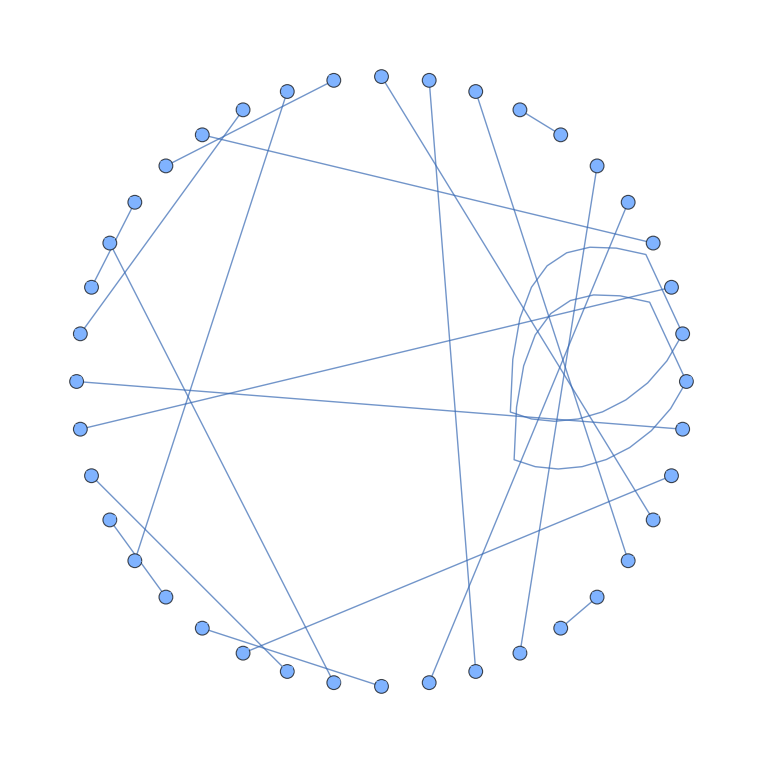

{1,40}

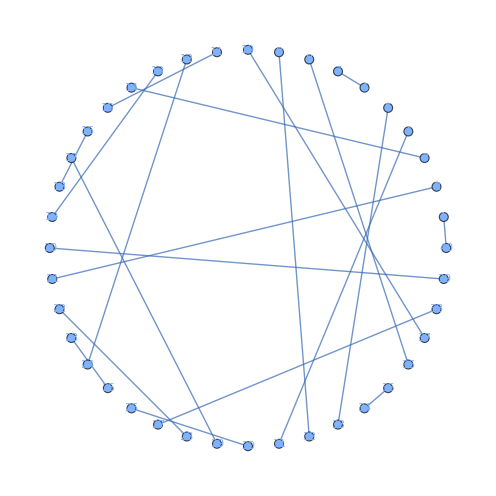

```mathematica
n=41
m=Table[Boole[Mod[i*j,n]==1],{i,1,n-1},{j,1,n-1}];
g=AdjacencyGraph[m];
GraphPlot[g,VertexCoordinates->circleLayout[n-1],VertexLabels->Placed[Automatic,Center]]
ex=Flatten@Position[Diagonal[m],1]
m[[ex[[1]],ex[[1]]]]=m[[ex[[2]],ex[[2]]]]=0;
m[[ex[[1]],ex[[2]]]]=m[[ex[[2]],ex[[1]]]]=1;
g=AdjacencyGraph[m];
GraphPlot[g,VertexCoordinates->circleLayout[n-1],VertexLabels->Placed[Automatic,Center]]
```

```mathematica
PrimePi[40]
```

12

41

{4,4,5,4,4,4,4,4,4,4,4,4,4,4,4,4,5,4,4,4,4,4,4,5,4,4,4,4,4,4,4,4,4,4,4,4,4,5,4,4}

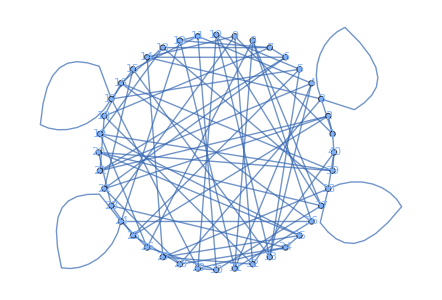

{{{5,10,33}},{{1,7,10,14,16,17,19,20,21,22,24,25,30,31,32,34,38}}}

```mathematica
n=41
m1=Table[Boole[Mod[i*j,n]==1],{i,1,n-1},{j,1,n-1}];
m1[[1,1]]=m1[[40,40]]=0;m1[[1,40]]=m1[[40,1]]=1;

m6=Table[Boole@MemberQ[{2,3,9},Mod[i*j,n]],{i,1,n-1},{j,1,n-1}];
(*m6[[8,8]]=m6[[33,33]]=m6[[20,20]]=m6[[21,21]]=m6[[13,13]]=m6[[28,28]]=0;m6[[8,33]]=m6[[33,8]]=m6[[20,21]]=m6[[21,20]]=m6[[13,28]]=m6[[28,13]]=1;*)
g=AdjacencyGraph[m1+m6];
VertexDegree[g]
GraphPlot[g,VertexCoordinates->circleLayout[n-1],VertexLabels->Placed[Automatic,Center]]
{FindClique[g],FindIndependentVertexSet[g]}
```